# Aula 1 - Preparação para Teste 1

# Diogo Nogueira A78957 Diogo Araújo A78485

## Questão 1

```mathematica
21^3456
```

3889399915469729073747248195097075377542292665860485606560698206610569749265475921852987005004986711069984842802116573371256669293381134897279436710702970268590742962864895005317390887875489236819003042434817662368003473785610546380934942200084574445884169521550558681050128742692048381691158615880368104391241695210591954883613325272498688122092793453331844130701453626130741027481843336242581469368347047754557322992860509072560234799704324898446321844454646658468059421369299423198857179839860893678278883760167787937663219533763639391021149222616448592937882921760041071169858673400345116093010739391524599047402296586057853023648813051958522906119646401561517492990920830324259191582151466950719055881930653302825074331167502761376357551956976936666527289143562159998258900633973791602250274316728244331931398335307051331238772091082238981216385216253857033238525086478461391240658361573935014098621370383597939146562455178710238190185204886000059059571920354151456738581483132434004748255263598289934111978799157434186679976095910373735645652440540527589351390550441086713204550322974766402860987332646926916366438635165728089199195342748827997898576670879737877717979083330827260491073901668128329904509723600761158409646999193335945231925516418796236439450362904575380893434204618266325128502660461299578081400716974356100953817633981703510114623623696478523949273824144584120933318861364597556490044646085669965697658161749016651239642439769886774171300908023533180653846618336487519878399729144684646403801122696610401176352945297622971787589655669952373276600164789310301589535570778949377748779545937873511406471883030143812326653952988981626598750675428514439385801849657327444839812399154956976137821977502826909281764515721167828066198863104030823023752699796434977749553155310045284534466407702358586568504676926943132442834437544083438834482029612605792452287142920135275129433789860069785224233018896838095852215755967872821499187766155897846336349395175965270917334997526400013115035974000443278409551650426388361878893573588737327504748535899717865277727515919468110012068026144185536708710603724296477544945198995012991297121165317953004538526203757048476189340672852366519698738159083405390981199677900507972710434611638983900206211608974717497971411230540878726385671884995173827990290693802340329411298181340102926417290953706270751549656028878290849313218695396857282107375207210857723383796875073322681985558616512985229777327441814468970885229233868314511965482129558057806626049425917559598106045850839547174333512046455895748194907982558584595436245491663153256466349641224542756566026421976146069539885151734859293014433293901085111678437728760154317842716380413554113591756912513816626664909246585004211094343845934601606690125754529827468824410576323749526251257560695203527813033144627155390398132146740298700763777617086313274484636655241954604400175149390738256784695319031296739365116990889324544871466084433417074489393154463443051282276276598530523764625712356851967252990015294986503068923421219036209332479728352756606033735146248596633903920374191250152915966348791329108513948927921415389777108655104340132164665810727741754949980830078145154121114954855967504352544500995068519788663833600019109368789171440863635566450535498115843392389925049267784348996357682034345737324163349018280941233311073363350184677569692148137966770707887749828997464592751480187367077952063631017463858708378390110285221430161606315762384404607353056750605174793832528558757366122504318031483888254391067664970132970752150596052629089668397915919491683310075946612537748146443340369699495686633630464078198049091243281373534689739443798043337405249362417082649038645294049165178521694289107145041225627278774881009546505788278373868898235756189460035380870169167452581205533159669849359089315827396018754864389825584901746065922780591793372117013444355411382051855680974135266157728599761194461575678787207427579942115351828170390139969686859247858746338967578261985043526354049459693886669343892766369815208199879412096662107566368638499701048557940296445005153369748558923842979120430916863109172104986597197018747387951394718750392389197777568816353506574889453858364578879173940883231794419136576142532566274121162681275698465751231492385780277463495964496179072062160962288675738909763264067639242125953207837779961452913401763467805651238396371701333470490357698327486254429605405742349055680840782261533259963511031314259159332178423722259178056682373965970575883546617501200110053609939884887629067914434592321471943341781674305811888325121

## Questão 2

```mathematica
DSolve[ x'[t] == x[t]^2,x[t],t]
```

{{x[t]→1/(-t-C[1])}}

```mathematica
DSolve[ {x'[t] == 2x[t],x[0]==-1},x[t],t]
```

{{x[t]→-ⅇ^(2 t)}}

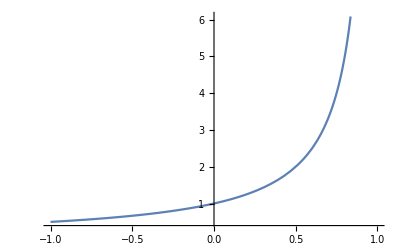

```mathematica
Plot[1/(1-t), {t,-1,1}]
```

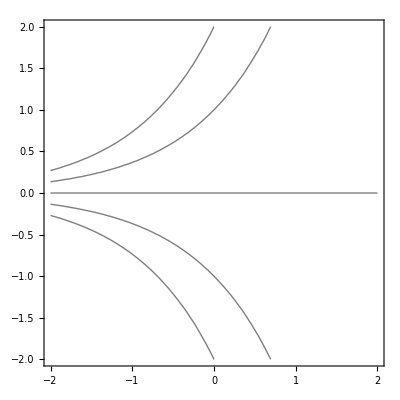

```mathematica
ContourPlot[x*Exp[-t],{t,-2,2},{x,-2,2}, ContourShading->False,Contours->{-2,-1,0,1,2},Axes->True]
```

```mathematica
DSolve[ x'[t] == 4t*Exp[-x[t]],x[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x[t]→Log[2 t^2+C[1]]}}

```mathematica
DSolve[ x'[t] == 4t*Exp[-x[t]],x[t],t]
```